```mathematica
Q = 0.7;
Clear[q]
```

```mathematica
S[k_,l_,r_,q_]:=Sqrt[k!/(2(2*l+k+1)!)]Exp[-q r]* (2q r)^(l+1)*LaguerreL[k,2l+1,2q r];
```

```mathematica
D[S[k,l,r,Q],r]
```

-0.989949 1.4^(1+l) ⅇ^(-0.7 r) r^(1+l) √((k!)/((1+k+2 l)!)) LaguerreL[-1+k,2+2 l,1.4 r]+(1.4^(1+l) ⅇ^(-0.7 r) (1+l) r^l √((k!)/((1+k+2 l)!)) LaguerreL[k,1+2 l,1.4 r])/(√2)-0.494975 1.4^(1+l) ⅇ^(-0.7 r) r^(1+l) √((k!)/((1+k+2 l)!)) LaguerreL[k,1+2 l,1.4 r]

```mathematica
Der[k_,l_,r_]:=-0.9899494936611664 1.4^(1+l) ⅇ^(-0.7 r) r^(1+l) √((k!)/((1+k+2 l)!)) LaguerreL[-1+k,2+2 l,1.4 r]+(1.4^(1+l) ⅇ^(-0.7 r) (1+l) r^l √((k!)/((1+k+2 l)!)) LaguerreL[k,1+2 l,1.4 r])/(√2)-0.4949747468305832 1.4^(1+l) ⅇ^(-0.7 r) r^(1+l) √((k!)/((1+k+2 l)!)) LaguerreL[k,1+2 l,1.4 r]
```

```mathematica
N[S[0,7,10,Q]]
N[S[8,2,10,Q]]
N[Der[0,6,10]]
N[Der[7,3,10]]
```

0.832143

-0.416306

-1.11022×10^-16

0.0573883

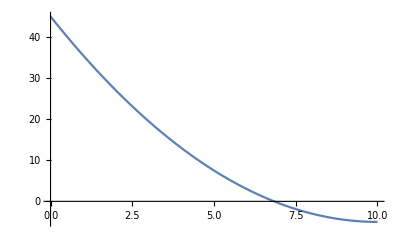

```mathematica
Plot[LaguerreL[2,8,r],{r,0,10}]
```

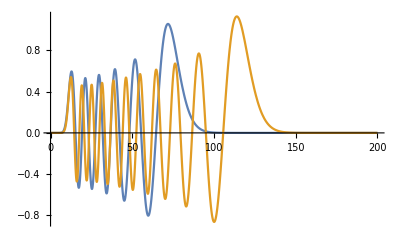

```mathematica
Plot[{S[10,20,r,Q],S[20,25,r,Q]},{r,0,200}]
```

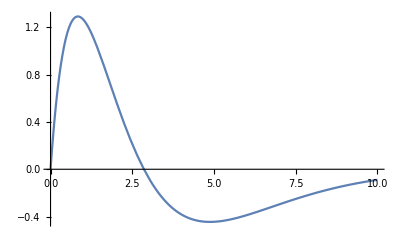

∫_0^10 (-1.96 ⅇ^(-0.7 r) r LaguerreL[-1+k,2,1.4 r]+1.4 ⅇ^(-0.7 r) LaguerreL[k,1,1.4 r]-0.98 ⅇ^(-0.7 r) r LaguerreL[k,1,1.4 r])ⅆr

```mathematica
Plot[Der[0,r],{r,0,10}]
Integrate[Der[r],{r,0,10}]
```

```mathematica
D[LaguerreL[k,2l+1,2q r],r]
```

-2 q LaguerreL[-1+k,2+2 l,2 q r]

```mathematica
DS[k_,l_,r_,q_]:=-2^(2+l) ⅇ^(-q r) q (q r)^(1+l) LaguerreL[-1+k,2+2 l,2 q r]+2^(1+l) ⅇ^(-q r) (1+l) q (q r)^l LaguerreL[k,1+2 l,2 q r]-2^(1+l) ⅇ^(-q r) q (q r)^(1+l) LaguerreL[k,1+2 l,2 q r];
```

```mathematica
D[r^2,r]
```

2 r

```mathematica
Integrate[S[1,1,r,Q],{r,0,100}]
```

-22.8571

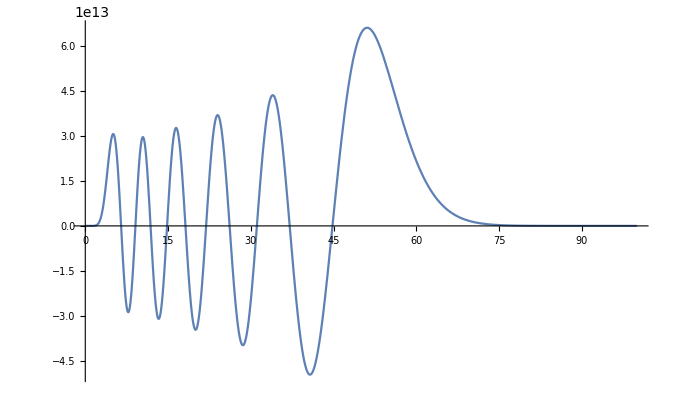

```mathematica
Plot[{S[10,10,r,Q]},{r,0,100}]
```